```mathematica
x=.; Remove["Global`*"];
Off[General::spell1];
```

```mathematica
conjugateRule={Complex[re_,im_]:>Complex[re,-im]};
conjugate[z_]:=z/.conjugateRule;
real[z_]:=(1/2)*(z+conjugate[z])//Simplify;
imag[z_]:=(-I/2)*(z-conjugate[z])//Simplify;
abs[z_]:=Sqrt[(z*(z/.conjugateRule))]//Simplify;
```

# simulation

## Constants

```mathematica
c=299792458 ;hb=1.0545715964207855*10^-34;q=1.602*10^-19;ϵ0=8.85*10^-12;m=9.1*10^-31;a0=4.0494*10^-10;den=4/a0^3;G0=Sqrt[(2^2)+(0)+(0)]*2*Pi/a0; 
normstructurefactor=1;atomscatfactor=5;re=2.82*10^-13*10^-2;ϵ0=8.85*10^-12;m=9.1*10^-31;
```

```mathematica
heV=4.135667662*10^-15;
```

```mathematica
atomscatfactor*normstructurefactor*4
```

20

## Scattering Factors (Aluminum). Data is hidden in this cell

```mathematica
aluminumdatan={{11000,0.999999},{9999.6101988112,0.9999946},{9500.05109608919,0.999994},{9000.08470202236,0.999993},{8000.07529068654,0.999991},{7000.06587935072,0.999989},{6000.05646801491,0.999984},{5000.00672884059,0.99998},{4000.03764534327,0.99997},{3500.03293967536,0.99995},{3000.02823400745,0.99994},{2500.00336442029,0.99991},{1999.98656066104,0.99987},{1900.01021921784,0.99986},{1799.99080813374,0.99985},{1700.01051465831,0.99984},{1674.99988996447,0.99984},{1594.99275548743,0.99986},{1579.99244131741,0.99987},{1564.00795790625,0.9999},{1561.99817142537,0.99992},{1559.99354355998,0.99993},{1558.99315790542,0.99992},{1557.99405447424,0.99992},{1553.99093632964,0.99991},{1552.00679528659,0.99991},{1550.00833673034,0.99989},{1539.9971041493,0.99987},{1520.00351671664,0.99985},{1499.99596954958,0.99983},{1450.00019711907,0.99981},{1399.99736740845,0.99979},{1300.00279801474,0.99974},{1200.01129360298,0.99968},{1100.03696970153,0.99961},{999.96101988112,0.99953},{900.008470202236,0.9994},{800.007529068654,0.99924},{700.006587935072,0.99898},{600.005646801491,0.9986},{500.000672884059,0.99797},{400.003764534327,0.99694},{300.002823400745,0.9948},{250.000336442029,0.99313},{199.998656066104,0.99111},{190.001021921784,0.99054},{179.999080813374,0.99007},{170.001051465831,0.98909},{159.999441038392,0.98912},{149.999596954958,0.98966},{145.000019711907,0.98934},{139.999736740845,0.98883},{134.999800584772,0.98793},{130.000279801474,0.98761},{125.000168221015,0.98941},{120.001129360298,0.99139},{115.003401219794,0.99233},{110.003696970154,0.99415},{105.000988190261,0.99285},{99.996101988112,0.99123},{97.9964960915745,0.99265},{96.0009034882385,0.99652},{93.999368351069,1.0012},{91.9976009906211,1.0041},{90.0008470202236,1.0058},{88.0013960217617,1.006},{85.9992833842408,1.0065},{84.0007905522087,1.0074},{82.000771729537,1.0077},{80.0007529068654,1.0075},{79.0016355645852,1.0075},{77.9977144281958,1.0078},{76.9998552074649,1.0095},{75.9992441185853,1.0106},{75.4994317714408,1.011},{75.0016132448491,1.0118},{74.5013621289869,1.0132},{73.998905911704,1.0151},{73.9018697353877,1.0156},{73.8006945565833,1.0161},{73.6997960263092,1.0167},{73.599173011433,1.0173},{73.4988243850021,1.0181},{73.3987490262018,1.0194},{73.2989458203133,1.0219},{73.1994136586728,1.0259},{73.1001514386298,1.0262},{73.0011580635068,1.0246},{72.8981460812912,1.0255},{72.7996986994657,1.0305},{72.7015168611821,1.0349},{72.599348199473,1.0305},{72.5017056634466,1.0249},{72.4000974336117,1.0226},{72.2987736049099,1.0206},{72.2019373719194,1.0192},{72.1011670476041,1.0179},{72.0508872937355,1.0174},{72.0006776161789,1.0169},{70.9987784773865,1.0108},{70.0006587935072,1.007},{68.0004205863325,1.0019},{65.9987048094645,0.99791},{63.9989505265369,0.99457},{61.9987833058606,0.99143},{60.0005646801491,0.98827},{54.9994086213281,0.97998},{50.0000672884059,0.97048},{45.0004235101118,0.95834},{40.0003764534327,0.94189},{35.0003293967536,0.91802},{30.0002823400745,0.88013},{25.0000336442029,0.81512},{19.9998656066104,0.67912},{19.0001021921784,0.63242},{17.9999080813374,0.57251},{17.0001051465831,0.49131},{15.9999441038392,0.37197},{15.7999244131741,0.34031},{15.5999354355998,0.30373},{15.5000833673034,0.28271},{15.399971041493,0.25936},{15.3000107180833,0.23344},{15.2000351671665,0.20569},{15.1000702547906,0.17943},{14.9999596954958,0.15065},{14.7999578455201,0.094517},{14.6000596854794,0.067041},{14.3999682762175,0.054863},{13.9999736740845,0.044168},{13.0000279801474,0.036437},{12.0001129360298,0.035753},{11.0003696970154,0.038468},{9.9996101988112,0.046304},{9.00008470202236,0.057167},{8.00007529068654,0.072505},{7.00006587935072,0.094236},{6.00005646801491,0.12677},{5.00000672884059,0.18137},{4.00003764534327,0.28003},{3.79996220592926,0.31474},{3.40002102931662,0.39877},{3.00002823400745,0.52135},{2.80002635174029,0.6079},{2.5999783348724,0.7278},{2.40002258720596,0.8734},{2.19999586307043,1.0728},{1.99998656066104,1.366},{1.90088412196336,1.5724},{1.79999080813374,1.8301},{1.70001051465831,2.1606},{1.59999441038392,2.6154},{1.55999354355998,2.7675},{1.52000351671664,2.7668},{1.47999578455201,2.6945},{1.39999736740845,2.2802},{1.3599934937922,1.9739},{1.32000220227259,1.6784},{1.2800054391776,1.4867},{1.24000046860683,1.4359},{1.20001129360298,1.3998},{1.10003696970153,1.3281},{0.999961019881119,1.3157},{0.900008470202236,1.3899},{0.800007529068654,1.5782},{0.700006587935072,1.9205},{0.600005646801491,2.4738},{0.500000672884059,3.3372},{0.450004235101118,3.938},{0.400003764534327,4.7097},{0.379996220592926,5.0735},{0.360003388080894,5.4903},{0.340002102931662,5.9564},{0.320003011627462,6.4808},{0.300002823400745,7.0796},{0.280002635174029,7.7757},{0.25999783348724,8.5881},{0.240002258720596,9.558},{0.219999586307043,10.742},{0.199998656066104,12.195},{0.179999080813374,14.088},{0.159999441038392,16.755},{0.139999736740845,20.837},{0.120001129360298,26.216},{0.0999961019881119,33.519},{0.0900008470202236,38.461},{0.0800007529068654,43.775},{0.0700006587935072,50.951},{0.0649987768571743,54.413},{0.0600005646801491,58.58},{0.0549994086213281,63.554},{0.0500000672884059,68.535},{0.0450004235101118,75.748},{0.0400003764534327,91.955},{0.0371959220157382,102.1},{0.030996291713765,125.14},{0.0278969415118036,140.05},{0.024797033371012,157.3},{0.0216969702602303,177.93},{0.0185979610078691,202.63},{0.0154979521324808,233.56},{0.0123990126460118,274.38},{0.0099188133484048,318.81},{0.00900008470202236,339.62},{0.00805883437471953,364.04},{0.00700006587935072,397.93},{0.006199258342753,423.96}};
```

```mathematica
aluminumdatak={{11000,2.241*^-8},{9999.6101988112,8.241*^-8},{9500.05109608919,1.272*^-7},{9000.08470202236,1.2488*^-7},{8000.07529068654,1.9173*^-7},{7000.06587935072,3.1463*^-7},{6000.05646801491,5.5102*^-7},{5000.00672884059,1.0726*^-6},{4000.03764534327,2.4843*^-6},{3500.03293967536,4.0484*^-6},{3000.02823400745,7.1408*^-6},{2500.00336442029,0.000013642},{1999.98656066104,0.000032079},{1900.01021921784,0.000038497},{1799.99080813374,0.000047138},{1700.01051465831,0.000057974},{1674.99988996447,0.000061633},{1594.99275548743,0.000074862},{1579.99244131741,0.00007848},{1564.00795790625,0.000085418},{1561.99817142537,0.000071847},{1559.99354355998,0.000049998},{1558.99315790542,0.000041131},{1557.99405447424,0.000032911},{1553.99093632964,0.000023687},{1552.00679528659,0.000011026},{1550.00833673034,6.0484*^-6},{1539.9971041493,6.1901*^-6},{1520.00351671664,6.4818*^-6},{1499.99596954958,6.8049*^-6},{1450.00019711907,7.8422*^-6},{1399.99736740845,8.94*^-6},{1300.00279801474,0.000011636},{1200.01129360298,0.000015628},{1100.03696970153,0.000021586},{999.96101988112,0.000031115},{900.008470202236,0.000046771},{800.007529068654,0.000072992},{700.006587935072,0.00011811},{600.005646801491,0.00022001},{500.000672884059,0.00043503},{400.003764534327,0.00096887},{300.002823400745,0.0023492},{250.000336442029,0.0041863},{199.998656066104,0.0075099},{190.001021921784,0.0084716},{179.999080813374,0.0096517},{170.001051465831,0.010987},{159.999441038392,0.013728},{149.999596954958,0.014773},{145.000019711907,0.015437},{139.999736740845,0.016304},{134.999800584772,0.017765},{130.000279801474,0.020606},{125.000168221015,0.023421},{120.001129360298,0.024063},{115.003401219794,0.024928},{110.003696970154,0.025452},{105.000988190261,0.024415},{99.996101988112,0.02992},{97.9964960915745,0.033061},{96.0009034882385,0.035883},{93.999368351069,0.035311},{91.9976009906211,0.033392},{90.0008470202236,0.030918},{88.0013960217617,0.028956},{85.9992833842408,0.028232},{84.0007905522087,0.026826},{82.000771729537,0.02546},{80.0007529068654,0.024476},{79.0016355645852,0.024501},{77.9977144281958,0.024757},{76.9998552074649,0.02518},{75.9992441185853,0.023853},{75.4994317714408,0.023955},{75.0016132448491,0.02402},{74.5013621289869,0.024343},{73.998905911704,0.024184},{73.9018697353877,0.024228},{73.8006945565833,0.024282},{73.6997960263092,0.024375},{73.599173011433,0.024499},{73.4988243850021,0.024831},{73.3987490262018,0.025432},{73.2989458203133,0.026018},{73.1994136586728,0.024227},{73.1001514386298,0.019564},{73.0011580635068,0.019145},{72.8981460812912,0.020012},{72.7996986994657,0.020072},{72.7015168611821,0.012476},{72.599348199473,0.0041164},{72.5017056634466,0.0036218},{72.4000974336117,0.0034141},{72.2987736049099,0.00344},{72.2019373719194,0.0034767},{72.1011670476041,0.0034877},{72.0508872937355,0.0035108},{72.0006776161789,0.0035249},{70.9987784773865,0.0034957},{70.0006587935072,0.0035425},{68.0004205863325,0.003673},{65.9987048094645,0.0038926},{63.9989505265369,0.0041092},{61.9987833058606,0.0042397},{60.0005646801491,0.0043696},{54.9994086213281,0.0050004},{50.0000672884059,0.0057469},{45.0004235101118,0.0066191},{40.0003764534327,0.0078466},{35.0003293967536,0.0093121},{30.0002823400745,0.011651},{25.0000336442029,0.015894},{19.9998656066104,0.02234},{19.0001021921784,0.02477},{17.9999080813374,0.027681},{17.0001051465831,0.032409},{15.9999441038392,0.044202},{15.7999244131741,0.04832},{15.5999354355998,0.053349},{15.5000833673034,0.056697},{15.399971041493,0.061407},{15.3000107180833,0.068348},{15.2000351671665,0.079959},{15.1000702547906,0.094223},{14.9999596954958,0.11041},{14.7999578455201,0.16589},{14.6000596854794,0.2342},{14.3999682762175,0.29293},{13.9999736740845,0.39115},{13.0000279801474,0.59086},{12.0001129360298,0.77163},{11.0003696970154,0.95677},{9.9996101988112,1.1555},{9.00008470202236,1.3775},{8.00007529068654,1.6366},{7.00006587935072,1.9519},{6.00005646801491,2.3563},{5.00000672884059,2.9029},{4.00003764534327,3.7081},{3.79996220592926,3.9165},{3.40002102931662,4.3957},{3.00002823400745,5.0008},{2.80002635174029,5.3676},{2.5999783348724,5.7781},{2.40002258720596,6.2418},{2.19999586307043,6.7839},{1.99998656066104,7.4052},{1.90088412196336,7.7354},{1.79999080813374,8.0601},{1.70001051465831,8.3565},{1.59999441038392,8.4914},{1.55999354355998,8.3866},{1.52000351671664,8.2573},{1.47999578455201,8.1878},{1.39999736740845,8.1134},{1.3599934937922,8.3058},{1.32000220227259,8.597},{1.2800054391776,9.0655},{1.24000046860683,9.4939},{1.20001129360298,9.8914},{1.10003696970153,10.969},{0.999961019881119,12.245},{0.900008470202236,13.784},{0.800007529068654,15.656},{0.700006587935072,17.991},{0.600005646801491,20.982},{0.500000672884059,25.004},{0.450004235101118,27.58},{0.400003764534327,30.737},{0.379996220592926,32.183},{0.360003388080894,33.814},{0.340002102931662,35.608},{0.320003011627462,37.595},{0.300002823400745,39.826},{0.280002635174029,42.367},{0.25999783348724,45.257},{0.240002258720596,48.593},{0.219999586307043,52.518},{0.199998656066104,57.156},{0.179999080813374,62.841},{0.159999441038392,69.857},{0.139999736740845,78.274},{0.120001129360298,88.197},{0.0999961019881119,101.28},{0.0900008470202236,108.96},{0.0800007529068654,118.39},{0.0700006587935072,129.49},{0.0649987768571743,136.09},{0.0600005646801491,144.23},{0.0549994086213281,153.45},{0.0500000672884059,164.81},{0.0450004235101118,181.78},{0.0400003764534327,199.99},{0.0371959220157382,208.1},{0.030996291713765,230.19},{0.0278969415118036,243.43},{0.024797033371012,258.26},{0.0216969702602303,275.34},{0.0185979610078691,295.42},{0.0154979521324808,321.08},{0.0123990126460118,354.35},{0.0099188133484048,391.71},{0.00900008470202236,408.92},{0.00805883437471953,429.62},{0.00700006587935072,458.5},{0.006199258342753,483.7}};
```

```mathematica
aluminumdatan1=ReplacePart[aluminumdatan,{ii_,1}->aluminumdatan[[ii,1]]/hb*q];
```

Part::pkspec1: The expression ii cannot be used as a part specification.

```mathematica
aluminumdatak1=ReplacePart[aluminumdatak,{ii_,1}->aluminumdatak[[ii,1]]/hb*q];
```

Part::pkspec1: The expression ii cannot be used as a part specification.

```mathematica
n[w_]:=Interpolation[aluminumdatan1,InterpolationOrder->3][w]
nn[w_]:=Interpolation[aluminumdatak1,InterpolationOrder->3][w]
```

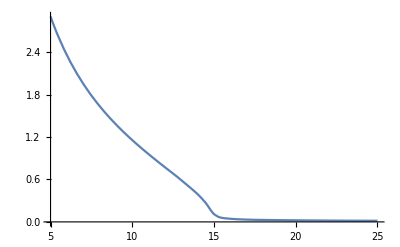

```mathematica
Plot[nn[Ei*q/hb],{Ei,5,25}]
```

```mathematica
epsR[w_]:=n[w]^2-nn[w]^2
```

```mathematica
epsI[w_]:=2*n[w]*nn[w]
```

```mathematica
k1z[w_,qi_]:=(√((w/c)^2-qi^2))
```

```mathematica
k2z[w_,qi_]:=(√(((w/c)*n[w])^2-qi^2))
```

```mathematica
rp[w_,qi_]:=((epsR[w]+epsI[w]*I)*k1z[w,qi]-k2z[w,qi])/((epsR[w]+epsI[w]*I)*k1z[w,qi]+k2z[w,qi])
```

```mathematica
Eres0=1.5;
wres0=Eres0*q/hb;
wp=Sqrt[(den*3*q^2)/(ϵ0*m)];
```

```mathematica
wp/(q/hb)
```

15.7975

```mathematica
γ=0.1*wp
```

2.3998×10^15

```mathematica
epsM[w_]:=1-wp^2/(w^2+I*γ*w)
```

```mathematica
nM[w_]:=(√((√((Re[epsM[w]])^2+(Im[epsM[w]])^2)+Re[epsM[w]])/2))
```

```mathematica
kM[w_]:=(√((√((Re[epsM[w]])^2+(Im[epsM[w]])^2)-Re[epsM[w]])/2))
```

```mathematica
nM[10*q/hb]
```

0.159157

```mathematica
αAbsM[w_]:=4*Pi*kM[w]*(w/c)/(2*Pi)
```

```mathematica
αAbs[w_]:=4*Pi*nn[w]*(w/c)/(2*Pi)
```

```mathematica
absLengthM[w_]:=1/αAbsM[w]
```

```mathematica
k2M[w_]:=(w/c)*√epsM[w]
```

```mathematica
k2Mz[w_,qi_]:=√(epsM[w]*(w/c)^2-qi^2)
```

```mathematica
Clear[rpM]
rpM[w_,qi_]:=(epsM[w]*k1z[w,qi]-k2Mz[w,qi])/(epsM[w]*k1z[w,qi]+k2Mz[w,qi])
```

# SPP dispersion vs dielectric light line

```mathematica
γ=0.12*wp;
θB400=Abs[ArcSin[2*G0/(2*kp0)]];
θs0=(θB400*180/Pi-0.04)*Pi/180;

Ep0=9978;
wp0=Ep0*q/hb;
kp0=wp0/c*n[wp0];
G=G0;
```

```mathematica
dBShift=0.02;
```

```mathematica
ip=9978;
```

```mathematica
kx[w_]:=w/c(√(epsM[w]/(epsM[w]+1)))
```

```mathematica
γ=0.12*wp;
```

```mathematica
kp0=n[ip*(q/hb)]*ip*(q/hb)/c;
```

```mathematica
ks[i_]:=n[ip*(q/hb)](ip-i)*(q/hb)/c;
```

```mathematica
kix[i_]:=Re[kx[i*q/hb]]
```

```mathematica
kpx[i_,dB_]:=ks[i]*Cos[θs0-(dB+dBShift)*Pi/180]-kix[i]
```

```mathematica
kpxLightLine[i_,dB_]:=ks[i]*Cos[θs0-(dB+dBShift)*Pi/180]-(i*(q/hb))/c
```

```mathematica
θp[i_,dB_]:=ArcCos[kpx[i,dB]/kp0]
```

```mathematica
θpLightLine[i_,dB_]:=ArcCos[kpxLightLine[i,dB]/kp0]
```

# Applying Newton’s method to solve for the angular SPP dispersion

```mathematica
initialGuess = 0.15; (* You may need to adjust the initial guess based on the expected solution range *)

solution = FindRoot[dB==-dBShift+(ArcCos[kpx[10,dB]/kp0]-θB400)*180/Pi, {dB, initialGuess}]
```

{dB→0.0672412}

```mathematica
bla=dB/.(FindRoot[dB==-dBShift+(ArcCos[kpx[10,dB]/kp0]-θB400)*180/Pi, {dB, initialGuess}])
```

0.0672412

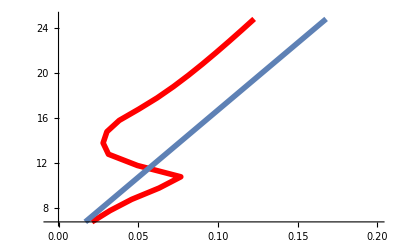

```mathematica
initialGuess = 0.05;
Ei1=6.78;
Ei2=25;

Show[ListPlot[Table[{dB/.(FindRoot[dB==-dBShift+(θp[i,dB]-θB400)*180/Pi, {dB, initialGuess}]),i},{i,Ei1,Ei2}],Joined->True,PlotRange->{{-0.005,0.20},{Ei1,Ei2}},PlotStyle->{Red,Thickness[0.01]},PlotLabel->None,LabelStyle->{16,GrayLevel[0],Bold}],ListPlot[Table[{dB/.(FindRoot[dB==-dBShift+(θpLightLine[i,dB]-θB400)*180/Pi, {dB, initialGuess}]),i},{i,Ei1,Ei2}],Joined->True,PlotRange->{{-0.005,0.20},{Ei1,Ei2}},PlotStyle->{(*Black,Dashed,*)Thickness[0.01]},PlotLabel->None,LabelStyle->{16,GrayLevel[0],Bold}]]
```

# QED simulation with γ=0.12*wp

```mathematica
µ0=1/(c^2 ϵ0);
η0=Sqrt[µ0/ϵ0]
```

376.909

```mathematica
ip=9978;
```

```mathematica
kp0=n[ip*(q/hb)]*ip*(q/hb)/c;
```

```mathematica
ks[i_]:=n[ip*(q/hb)](ip-i)*(q/hb)/c;
```

```mathematica
γ=0.12*wp;
θB400=Abs[ArcSin[2*G0/(2*kp0)]];
θs0=(θB400*180/Pi-0.04)*Pi/180;
Lz=3*10^-8;
xs=0;
dBShift=0(*0.048*);

j0=25
Ep0=9978;
wp0=Ep0*q/hb;
wi0=j0*q/hb;
ws0=wp0-(j0*q/hb);
kp0=wp0/c*n[wp0];
ks0=ws0/c*n[ws0];
ki0=wi0*n[wi0]/c; 
G=G0;

θB=Abs[ArcSin[2*G0/(2*kp0)]];
```

25

```mathematica
Re[k2M[25*q/hb]]
```

9.83998×10^7

```mathematica
Abs[k2M[25*q/hb]]
```

9.84304×10^7

```mathematica
βs[j_,dB_,xs_]:=η0/(2*hb*(wp0-(j*q/hb)))1/(Cos[θs0+xs-(dB+dBShift)*Pi/180])^2;
```

```mathematica
βs[22]
```

βs[22]

```mathematica
idlerNorm[j_]:=(hb*(j*q/hb)^2)/(Pi*ϵ0*c^2);
```

```mathematica
idlerNorm[20]
```

3.8956×10^-8

```mathematica
pumpPreFactor=2*hb*η0*wp0/Sin[θB400];
```

```mathematica
ρG=q*(den*3*atomscatfactor*normstructurefactor);
```

```mathematica
σs[j_]:=(q^2*ρG)/(m^2*wp0*(j*q/hb)^2);
```

```mathematica
σs[22]
```

2.64994×10^-19

```mathematica
ws[j_]:=wp0-(j*q/hb);
```

```mathematica
ηs=1/(ϵ0*c);ηp=1/(ϵ0*c)
```

376.909

```mathematica
χG[j_]:=(q*ρG)/(ϵ0*(j*q/hb)^2);
```

```mathematica
σNLSquared[j_]:=((0.01)^2*q^2*ϵ0^2*(2*G0)^2(Cos[2*θB])^2)/(4*m^2*(ws[j])^2);
```

```mathematica
(βs[10,0,0])*pumpPreFactor*(σs[10])^2*(idlerNorm[10])*(2*G0)^2*10^13*(ks[10])^2
```

5.84605×10^17

```mathematica
flux0=10^13;(* at 10 KeV per 0.1% BW *)
```

```mathematica
BW0=0.1*0.01; (*per 0.1% BW. This is equivalent to 10eV/10KeV*)
```

```mathematica
BWmonochromator=N[2/10000];(* 2eV/10KeV *)
```

```mathematica
PositiveSolutions=((1-Erf[(qiiXZ+(2*q/hb)/c)/(0.0005(25*q/hb)/c)])/2);
```

```mathematica
ScatteringDumping=((1-Erf[(qiiXZ+(2*q/hb)/c)/(0.0005(25*q/hb)/c)])/2)(1+Erf[(qiiXZ+(21*q/hb)/c)/(0.3(25*q/hb)/c)])/2;
```

```mathematica
func[dB_,i_,ii_,xs_,ys_,θg_]:=((q/hb)(βs[i+ii,dB,xs])*pumpPreFactor*(σs[i+ii])^2*(idlerNorm[i+ii])*(2*G0)^2*(flux0*(BWmonochromator/BW0))*(ks[i+ii])^2*Cos[θs0+xs-(dB+dBShift)*Pi/180]*((Abs[qii]/Abs[k2M[(i+ii)*q/hb]])^2)*(Abs[PositiveSolutions*(Re[1/k2Mz[(i+ii)*q/hb,qii]] Abs[(1-ⅇ^(I(dkzPS+ Re[k2Mz[(i+ii)*q/hb,qii]]) Lz-Im[k2Mz[(i+ii)*q/hb,qii]]Lz))/(I(dkzPS+ Re[k2Mz[(i+ii)*q/hb,qii]])-Im[k2Mz[(i+ii)*q/hb,qii]])]^2+Re[1/k2Mz[(i+ii)*q/hb,qii]] Abs[(1-ⅇ^(-I(dkzPS- Re[k2Mz[(i+ii)*q/hb,qii]]) Lz-Im[k2Mz[(i+ii)*q/hb,qii]]Lz))/(-I(dkzPS- Re[k2Mz[(i+ii)*q/hb,qii]])-Im[k2Mz[(i+ii)*q/hb,qii]])]^2)+ScatteringDumping*Re[(rpM[(i+ii)*q/hb,qii]/k2Mz[(i+ii)*q/hb,qii])(1-ⅇ^(I(dkzPS+ Re[k2Mz[(i+ii)*q/hb,qii]]) Lz-Im[k2Mz[(i+ii)*q/hb,qii]]Lz))/(I(dkzPS+ Re[k2Mz[(i+ii)*q/hb,qii]])-Im[k2Mz[(i+ii)*q/hb,qii]])(1-ⅇ^(-I(dkzPS- Re[k2Mz[(i+ii)*q/hb,qii]]) Lz-Im[k2Mz[(i+ii)*q/hb,qii]]Lz))/(-I(dkzPS- Re[k2Mz[(i+ii)*q/hb,qii]])-Im[k2Mz[(i+ii)*q/hb,qii]])]]))/.{(*j->i+ii,*)qiiXZ->(kp0*Cos[-(θB400*180/Pi+(dB+dBShift))*Pi/180]-2*G0*Sin[θg*Pi/180]-ks[i+ii]*Cos[θs0+xs-(dB+dBShift)*Pi/180]),qii->(*(kp0*Cos[-(θB400*180/Pi+(dB+dBShift))*Pi/180]-ks[i+ii]*Cos[θs0+xs-(dB+dBShift)*Pi/180])*)Sqrt[(kp0*Cos[-(θB400*180/Pi+(dB+dBShift))*Pi/180]-2*G0*Sin[θg*Pi/180])^2-2*(kp0*Cos[-(θB400*180/Pi+(dB+dBShift))*Pi/180]-2*G0*Sin[θg*Pi/180])*(ks[i+ii]*Cos[θs0+xs-(dB+dBShift)*Pi/180])*Cos[ys]+(ks[i+ii]*Cos[θs0+xs-(dB+dBShift)*Pi/180])^2],dkzPS->kp0*Sin[-(θB400*180/Pi+(dB+dBShift))*Pi/180]+2*G0*Cos[θg*Pi/180]-ks[i+ii]*Sin[θs0+xs-(dB+dBShift)*Pi/180]}
```

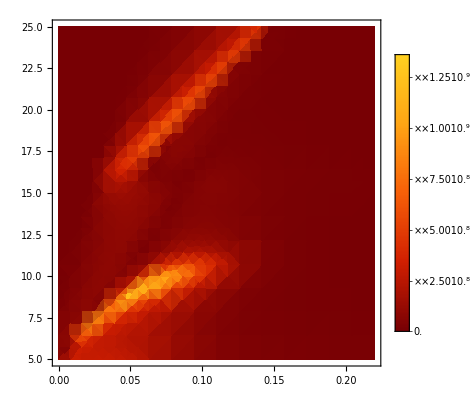

```mathematica
DensityPlot[func[dB,i,0,0,0,0.021],{dB,0,0.22},{i,5,25},PlotRange->All,PlotLegends->Automatic,PerformanceGoal->"Quality",ColorFunction->"SolarColors"]
```

```mathematica
Clear[dataMap1];
dataMap1=ParallelTable[
{dB,i,NIntegrate[Abs[func[dB,i,ii,xs,ys,0.021]],{ii,-0.75,0.75},{xs,-6*10^-4,6*10^-4},{ys,-6*10^-4,6*10^-4},Method->{"QuasiMonteCarlo","MaxPoints"->1*10^3}]},
{dB,-0.005,0.22,0.01},{i,6.78,25,0.2}]
```

NIntegrate::maxp: The integral failed to converge after 1000 integrand evaluations. NIntegrate obtained 74.7644 and 1.06555 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000 integrand evaluations. NIntegrate obtained 75.36 and 1.12194 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000 integrand evaluations. NIntegrate obtained 76.8326 and 1.19789 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000 integrand evaluations. NIntegrate obtained 25.2152 and 0.267419 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000 integrand evaluations. NIntegrate obtained 25.076 and 0.288393 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000 integrand evaluations. NIntegrate obtained 25.2357 and 0.318606 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 633 integrand evaluations. NIntegrate obtained 10.9722 and 0.110319 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 742 integrand evaluations. NIntegrate obtained 10.9633 and 0.112502 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 907 integrand evaluations. NIntegrate obtained 11.0308 and 0.114086 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000 integrand evaluations. NIntegrate obtained 9.10589 and 0.097439 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000 integrand evaluations. NIntegrate obtained 8.15252 and 0.0903891 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000 integrand evaluations. NIntegrate obtained 7.25105 and 0.0809948 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

```mathematica
Clear[dataMap2];
dataMap2=Partition[Flatten[dataMap1],3]
```

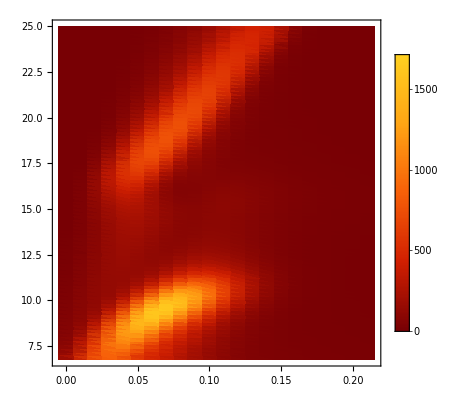

```mathematica
ListDensityPlot[dataMap2,PlotRange->All,PlotLegends->Automatic,ColorFunction->"SolarColors",PlotLabel->None,LabelStyle->{16,GrayLevel[0],Bold}]
```

```mathematica
N[2700/200]
```

13.5

# 2D dispersion plot on top of QED plot

```mathematica
γ=0.12*wp;
```

```mathematica
dBShift=0.02;
```

General::prng: Value of option PlotRange -> {{-0.005,dBmax},{6.78,25}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

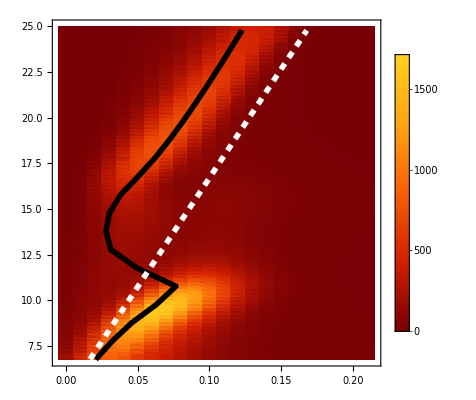

```mathematica
Show[ListDensityPlot[dataMap2,PlotRange->All,PlotLegends->Automatic,ColorFunction->"SolarColors",PlotLabel->None,LabelStyle->{16,GrayLevel[0],Bold}],ListPlot[Table[{dB/.(FindRoot[dB==-dBShift+(θp[i,dB]-θB400)*180/Pi, {dB, initialGuess}]),i},{i,Ei1,Ei2}],Joined->True,PlotRange->{{-0.005,dBmax},{Ei1,25}},PlotStyle->{Black,Thickness[0.01]},PlotLabel->None,LabelStyle->{16,GrayLevel[0],Bold}],ListPlot[Table[{dB/.(FindRoot[dB==-dBShift+(θpLightLine[i,dB]-θB400)*180/Pi, {dB, initialGuess}]),i},{i,Ei1,Ei2}],Joined->True,PlotRange->{{-0.005,dBmax},{Ei1,Ei2}},PlotStyle->{White,Dashed,Thickness[0.01]},PlotLabel->None,LabelStyle->{16,GrayLevel[0],Bold}]]
```

```mathematica
Export["E:\\Haim\\for SPP paper 2024-2025\\Al400_DensityMap_with_Kinematics.png",%,"PNG",ImageResolution->900]
```

# Energy spectrum

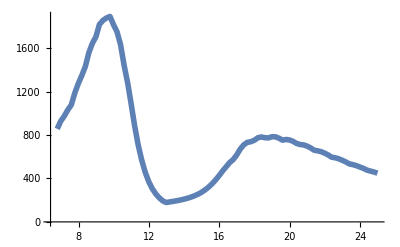

```mathematica
(*Step 1:Flatten the data to make it easier to work with*)flatData=Flatten[dataMap1,1];

(*Step 2:Group data by each unique i value*)
groupedData=GatherBy[flatData,#[[2]]&];

(*Step 3:For each group (corresponding to each i),find the maximum intensity*)
maxIntensitiesForI=Table[{group[[1,2]],Max[group[[All,3]]]},(*Take the max intensity within each group of i*){group,groupedData}];

(*Step 4:Plot the maximum intensity for each i*)
ListLinePlot[maxIntensitiesForI,Joined->True,PlotRange->All,PlotStyle->Thickness[0.01],PlotLabel->None,LabelStyle->{16,GrayLevel[0],Bold}]
```

```mathematica
Export["E:\\Haim\\for SPP paper 2024-2025\\Al400_Spectrum.png",%,"PNG",ImageResolution->900]
```